# Mathematica Basics

Below is a tutorial on the most very basic features of Mathematica. It is an extremely powerful tools great for graphics and analytical problems. I don’t believe that handling data is one of Mathematica’s stronger aspects, but I encourage you to dive in deeper and discover some of its data handling methods for yourself
I modified this notebook from one given to me by Brent Nelson.

CONTENTS

### 1. Simple Exercise Plotting Functions and Data points

### 2. Simple Exercises: Algebra, Derivatives, Integrals, Series

### 3. Simple Exercises: Defining Functions

Simple Exercise Plotting Functions and Data points

On the top toolbar you will find the HELP section. You can literally copy and
paste the examples in the HELP section into this notebook and compile them. To 
erase the memory of the session, go on the top tool bar:
 KERNEL → quit Kernal → local .

Suppose you wish to plot a simple trig function. Simply type the following 
and hit enter (notice the "cell" brackets to the very far left in blue. Everything 
has its own "cell". Double click on the various brackets to see what happens, you can
"minimize" sections by doing this.)

```mathematica
P1=Plot[Sin[x],{x,0,2π},PlotStyle->Hue[.6]];
```

```mathematica
P2=Plot[Cos[x],{x,0,2π},PlotStyle->Hue[.9]];
```

```mathematica
Show[P1,P2];
```

Some useful shortcuts are 
esc theta esc which gives:   θ
x control ^3   which gives:   x^3
 control /  which gives after you fill in the boxes:   a/b

When graphing, you can set some options.

```mathematica
Fancy ={Frame->True,FrameLabel->{"θ","sin^2/(a  θ)^2","Intensity   Distribution",""}
,RotateLabel->False, Axes-> False,PlotRange-> All,FormatType-> TraditionalForm,
PlotStyle->Hue[.7]};
```

```mathematica
a=1.1
```

1.1

```mathematica
Plot[(Sin[ a  θ]/(a  θ))^2,{θ,-4π,4π},Evaluate[Fancy]];
```

If you have a set of points and no function, create some points using Table that should trace out the above curve

Below is a  list of y values .  
If you remove the semi-colon below you will see a ton of points.  
You may not want to see them so I suppress
them with a semi-colon at the end, much like in MATLAB.

```mathematica
y = Table[(Sin[ a  θ]/(a  θ))^2,{θ,-4π,4π,.01}];
```

To delete the points after you viewed them , highlight the bracket that they are in 
and delete that bracket.
Create an array of x values .

```mathematica
x= Table[a  θ,{θ,-4π,4π,.01}];
```

Finally group them in to a list of x, y pairs. (Notice that the indexing of an array requires double brackets [[ ]])

```mathematica
DatatoPlot = Table[{x⟦n⟧,y⟦n⟧},{n,1, Length[x]}];
```

```mathematica
ListPlot[DatatoPlot,Evaluate[Fancy]];
```

```mathematica
Length[x]
```

2514

```mathematica
Length[y]
```

2514

This plot has 2514 {x,y} pairs on it. 
This first pair plotted:

```mathematica
{x⟦1⟧,y⟦1⟧}
```

{-13.823,0.00473377}

This last pair plotted is

```mathematica
{x⟦ 2514⟧,y⟦2514⟧}
```

{13.82,0.00472652}

Simple Exercises:  Algebra, Derivatives, Integrals, Series

```mathematica
x=.
```

```mathematica
a=.
```

That cleared the value of x and a from above. Of course keep in mind that Mathematica sees x and X as different variables

```mathematica
Solve[a X^2+ b X +c ==0,X]
x
```

{{X→(-b-√(b^2-4 a c))/(2 a)},{X→(-b+√(b^2-4 a c))/(2 a)}}

x

How about simultaneous equations?

```mathematica
Solve[{X^2 + 2 Y X ==4, Y==4},{X,Y}]
```

{{Y→4,X→2 (-2-√5)},{Y→4,X→2 (-2+√5)}}

Here is a physics one:

```mathematica
Solve[{ℰsquared ==(p c)^2 +  (m c^2)^2,p== (m v)/(√(1-v^2/c^2))},v]
```

{{v→-(c p)/(√(c^2 m^2+p^2))},{v→(c p)/(√(c^2 m^2+p^2))}}

Try on the top tool bar file → Palettes  → Basic Math Assistant to insert some special characters
We will take a partial derivative

```mathematica
D[(ⅇ^(- β Subscript[ℰ, n])), β]
```

-ⅇ^(-β ℰ_n) ℰ_n

Again file → Palettes  → Basic Math Assistant allows you to insert special characters, but there are also keyboard shortcuts for most of them:
esc ee  esc = ⅇ
esc inf esc = ∞  
esc e esc =  ϵ 
esc p esc = π

 Define a function (note the underscore for β__ 
 that's a little weird thing in Mathematica )

```mathematica
Z[β_,𝒩_]=-∑_(n=0)^𝒩 ⅇ^(-β Subscript[ϵ, n]);
```

```mathematica
Z[10,1]
```

-ⅇ^(-10 ϵ_0)-ⅇ^(-10 ϵ_1)

```mathematica
D[Log[Z[β,∞]], β]
```

(∑_(n=0)^∞ -ⅇ^(-β ϵ_n) ϵ_n)/(∑_(n=0)^∞ ⅇ^(-β ϵ_n))

Mathematica integrate functions numerically and analytically

```mathematica
∫_0^π Sin[(n π x)/L ]ⅆx
```

(L-L Cos[(n π^2)/L])/(n π)

How about a nasty one?

```mathematica
∫_0^π x^3 Sin[(n π x)/L ]ⅆx
```

(L ((6 L^2 n π^2-n^3 π^6) Cos[(n π^2)/L]+3 L (-2 L^2+n^2 π^4) Sin[(n π^2)/L]))/(n^4 π^4)

How about one you really never want to do, ever.

```mathematica
∫_(L/64)^ω ( Sin[(n π x)/L ])^13 ⅆx
```

1/(12300288 n π)(L (5153148 Cos[(n π)/64]-1288287 Cos[(3 n π)/64]+429429 Cos[(5 n π)/64]-122694 Cos[(7 n π)/64]+26026 Cos[(9 n π)/64]-3549 Cos[(11 n π)/64]+231 Cos[(13 n π)/64]-5153148 Cos[(n π ω)/L]+1288287 Cos[(3 n π ω)/L]-429429 Cos[(5 n π ω)/L]+122694 Cos[(7 n π ω)/L]-26026 Cos[(9 n π ω)/L]+3549 Cos[(11 n π ω)/L]-231 Cos[(13 n π ω)/L]))

Here is classic, that you have to do in the complex plane

```mathematica
∫_(-∞)^∞ (Sin[x]/x)^2 ⅆx
```

π

How about a limit?

```mathematica
Limit[ (Sin[x]/x)^2,x-> 0]
```

1

Here is a triple integral (giving the volume of a sphere)

```mathematica
∫_0^(2π) (∫_0^π (∫_0^R r^2 Sin[θ]ⅆr)ⅆθ)ⅆϕ
```

(4 π R^3)/3

How about an n-dimensional sphere? First, the factorial function is built in

```mathematica
23!
```

25852016738884976640000

You can derive the volume of  n-dimensional sphere
 (see Pathria Statistical Mechanics for a good derivation)

```mathematica
V[n_]=(π^(n/2)R^n)/Gamma[n/2+1];
```

n=0 is a point.

```mathematica
V[0]
```

1

n=1 is the circumference of a circle (or an unrolled line)

```mathematica
V[1]//FullSimplify
```

2 R

n=2 is the area of a circle

```mathematica
V[2]
```

π R^2

n=3 is the volume of a 3-sphere.

```mathematica
V[3]
```

(4 π R^3)/3

I leave you to interpret n > 3.

We will next form a series. Use Normal to capture the useful terms.

```mathematica
Series[Log[1+u],{u,0,22}]
h[u_] = Normal[Series[Log[1+u],{u,0,22}]]
```

u-u^2/2+u^3/3-u^4/4+u^5/5-u^6/6+u^7/7-u^8/8+u^9/9-u^10/10+u^11/11-u^12/12+u^13/13-u^14/14+u^15/15-u^16/16+u^17/17-u^18/18+u^19/19-u^20/20+u^21/21-u^22/22+O[u]^23

u-u^2/2+u^3/3-u^4/4+u^5/5-u^6/6+u^7/7-u^8/8+u^9/9-u^10/10+u^11/11-u^12/12+u^13/13-u^14/14+u^15/15-u^16/16+u^17/17-u^18/18+u^19/19-u^20/20+u^21/21-u^22/22

Lets check it numerically

```mathematica
u=.3456;
h[u]
```

0.29684

```mathematica
Log[1+u]
```

0.29684

Mathematica can handle complex numbers (use esc i esc to get =   ⅈ)

```mathematica
ⅈ^2
```

-1

Lets check the very very useful identity :   ⅇ^(ⅈ θ) = Cos[θ]+ⅈ Sin[θ]

```mathematica
Series[ⅇ^(ⅈ θ),{θ,0,6}]
```

1+ⅈ θ-θ^2/2-(ⅈ θ^3)/6+θ^4/24+(ⅈ θ^5)/120-θ^6/720+O[θ]^7

```mathematica
Series[Cos[θ]+ⅈ Sin[θ],{θ,0,6}]
```

1+ⅈ θ-θ^2/2-(ⅈ θ^3)/6+θ^4/24+(ⅈ θ^5)/120-θ^6/720+O[θ]^7

```mathematica
Series[Cos[θ],{θ,0,6}]
```

1-θ^2/2+θ^4/24-θ^6/720+O[θ]^7

```mathematica
Series[Sin[θ],{θ,0,6}]
```

θ-θ^3/6+θ^5/120+O[θ]^7

```mathematica
ⅇ^(ⅈ θ)//ExpToTrig
```

Cos[θ]+ⅈ Sin[θ]

Simple Exercises: Creating Functions

Let’s look at Problem 8 in Mathematica. We looked at an integral involving a pendulum subject to a particular potential V(x).

```mathematica
F[V_,a_:4]:= NIntegrate[(√8)/(√(V[a]-V[x])),{x,0,a}];
```

```mathematica
V[x_]:=x^4;
```

```mathematica
F[V,3]
```

1.23605

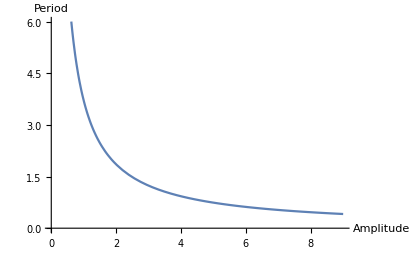

```mathematica
Plot[F[V,x],{x,0.01,9},AxesLabel->{"Amplitude","Period"},PlotRange->{{0,9},{0,6}}]
```

```mathematica
V[x_]:=x^2;
```

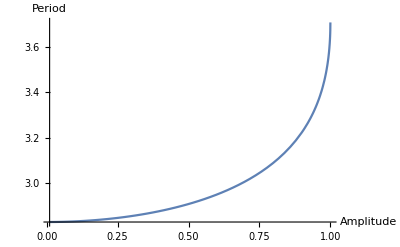

```mathematica
Plot[F[V,x],{x,0.01,1},AxesLabel->{"Amplitude","Period"}]
```

Let’s take a look at a projectile motion problem,

```mathematica
path[t_,v_,angle_,h_:0,g_:9.8]:= -0.5g t^2+v t Sin[angle Degree]+h;
Flight[v_,angle_,h_:0,g_:9.8] :={time=Solve[-0.5*g*t^2+v*Sin[angle Degree]*t+h==0,t][[2]];,v*Cos[angle Degree]*t/.time};
```

```mathematica
r=Flight[45,45]
```

{Null,206.633}

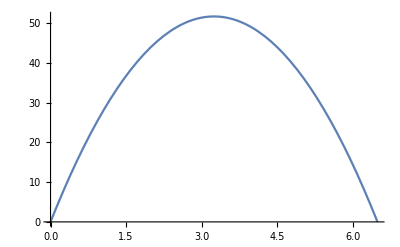

```mathematica
Plot[path[t,45,45,0,9.8],{t,0,t/.r[[1]]}]
```

```mathematica
D[path[t,45,45,0,9.8],t]
```

45/(√2)-9.8 t

```mathematica
time = Solve[-0.5*9.8*t^2+45*Sin[45 Degree]*t==0,t]
```

{{t→0.+0. ⅈ},{t→6.49384}}

```mathematica
time[[2]]
```

{t→6.49384}

```mathematica
5*time[[2]]
```

{5 (t→6.49384)}

```mathematica
5*t/.time[[2]]
```

32.4692

```mathematica
time
```

{t→6.49384}

```mathematica
Clear[time]
```